Upload the data into Mathematica..(this data has had the header rows and columns removed.)

```mathematica
tet1=Import["F:\\Papers Thesis\\Update to date Code and Paper\\HistFWDPricesForMathematica.xlsx"];
```

```mathematica
Dimensions[tet1];
```

The initial historic forward curve data

```mathematica
test2 = tet1[[1]];
dat2=Table[Table[{test2[[j,i]]},{i,1,24}],{j,1,270}];
ListPlot3D[test2,AxesLabel->{Maturity Months,Historic Days,Price NBP},PlotLabel->"Historic Forward Curve data",ColorFunction->"Rainbow"];
```

Find the covariance matrix and plot the results

```mathematica
meanvecdata1=Round[Mean[test2],.001];
covmatdata1=Round[Covariance[test2],.001];
```

```mathematica
ListPlot3D[Covariance[covmatdata1],AxesLabel->{Maturity ,Maturity,Covariance},PlotLabel->"Covariance Surface",ColorFunction->"Rainbow"];
```

```mathematica
Eigenvalues[covmatdata1];
Eigenvectors[covmatdata1];
```

```mathematica
ListPlot[Eigenvalues[covmatdata1],PlotLabel->"Eigenvalues Surface",Joined->True, Mesh->All,PlotRange->All];
```

```mathematica
Variance[pc=PrincipalComponents[test2]];
```

```mathematica
{λ,V}=Eigensystem[Covariance[test2]];
```

```mathematica
pca = PrincipalComponents[test2]
```

{{48.9464,0.192127,0.425903,0.0786216,0.874816,0.170827,0.856863,0.540663,0.502095,0.270175,0.0252588,0.280004,0.0167778,0.212924,0.0281066,0.198029,0.125869,0.00545993,0.0420015,0.0211407,0.0131051,0.0101825,0.0299716,0.00514336},269}
 |  |  |  |

```mathematica
(*take the principal components and sample the forward curve....*)
```

Charting the principal components as per c# code

```mathematica
pcasharp = {{-6.26080273795713,-0.309211138757538,-0.247647112912254,-0.118054358426137,-0.0798938459419098,-0.0706024496378116,-0.0484641910666792,-0.0392353088810048,-0.0341064874385374,-0.0348404143946913,-0.0274874154071027,-0.0243732760412726,-0.0243962204145349,-0.0182818541300883,-0.0157127411677281,-0.010589574337276,-0.0102203298479903,-0.00754659288459697,-0.00645276981583925,-0.00433404120980307,-0.00386798319888784,-0.00374708815281179,-0.00294962941972741,-0.00261007718667042},{11.7512639653751,0.613141273096998,0.363639850308737,0.155840663630286,-0.0649756620675788,-0.0175751533206642,-0.0236270235274091,-0.000737606215412154,-0.0302147935891628,-0.00193773818380527,-0.00146796102621506,-0.00461976204556492,-0.00202249751564096,-0.000700785282989424,-0.00641944963541263,-0.0343047852922044,-0.00127405855882569,-0.00153508784422771,-0.00484907978505961,-0.00392581083160877,-0.00376691046338819,-0.000045704529578678,0.000065020395739597,-.000040242171767647},{3.06837055856713,0.193560092145475,0.275914411745451,0.15210899531994,0.113855104065373,0.0297868787152026,0.0599718029827919,0.0192547105670648,0.0466140538024386,-0.00325013185783244,-0.00394239740675222,0.000355275331959283,-0.00746420585305918,-0.00935051228249918,-0.00569984486200937,0.026937417758987,-0.0120702461755998,-0.00711598929216941,-0.00241287350973008,-0.00172981557851152,-0.0024028403189341,-0.00612397591439825,-0.00487367154084499,-0.00380679439360472}}
```

{{-6.2608,-0.309211,-0.247647,-0.118054,-0.0798938,-0.0706024,-0.0484642,-0.0392353,-0.0341065,-0.0348404,-0.0274874,-0.0243733,-0.0243962,-0.0182819,-0.0157127,-0.0105896,-0.0102203,-0.00754659,-0.00645277,-0.00433404,-0.00386798,-0.00374709,-0.00294963,-0.00261008},{11.7513,0.613141,0.36364,0.155841,-0.0649757,-0.0175752,-0.023627,-0.000737606,-0.0302148,-0.00193774,-0.00146796,-0.00461976,-0.0020225,-0.000700785,-0.00641945,-0.0343048,-0.00127406,-0.00153509,-0.00484908,-0.00392581,-0.00376691,-0.0000457045,0.0000650204,-0.0000402422},{3.06837,0.19356,0.275914,0.152109,0.113855,0.0297869,0.0599718,0.0192547,0.0466141,-0.00325013,-0.0039424,0.000355275,-0.00746421,-0.00935051,-0.00569984,0.0269374,-0.0120702,-0.00711599,-0.00241287,-0.00172982,-0.00240284,-0.00612398,-0.00487367,-0.00380679}}

```mathematica
Clear[pcasharp]
```

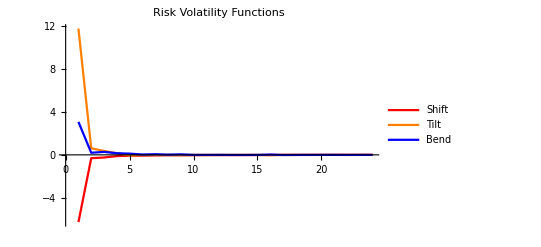

```mathematica
ListLinePlot[{pcasharp[[1]],pcasharp[[2]],pcasharp[[3]]},PlotLabel->"Risk Volatility Functions",PlotStyle->{Red,Orange,Blue},PlotLegends->{"Shift","Tilt","Bend"},PlotRange->All]
```

Charting the simulations of the forward curve at time point 1 day and 10 days....

```mathematica
simday1=Import["F:\\Papers Thesis\\Update to date Code and Paper\\1daysimulation.xlsx"];
simday10 =Import["F:\\Papers Thesis\\Update to date Code and Paper\\10simulation.xlsx"];
```

{{{45.92,46.13,44.82,42.67,41.02,39.76,40.37,40.62,40.65,42.01,44.97,46.71,47.71,47.62,46.5,43.83,40.36,40.29,40.79,41.07,41.24,42.36,45.93,47.31},{1},997,{1},{0.,1.17658×10^-235,6.04673×10^-157,1.53907×10^-60,22611.5,1.12985×10^15,1839.51,2.77761×10^6,139724.,6,530719.,3.04111×10^7,455861.,116668.,13624.3,14084.8,13370.5,4251.15,2058.95}}}
 |  |  |  |

```mathematica
sim1 = simday1[[1]];
sim10 = simday10[[1]];
ListPlot3D[sim1,AxesLabel->{Maturity Months,Historic Days,Price NBP},PlotLabel->"Forward Curve data Simulation time stamp 1 day",ColorFunction->"Rainbow"]
ListPlot3D[sim10,AxesLabel->{Maturity Months,Historic Days,Price NBP},PlotLabel->"Forward Curve data Simulation time stamp 10 days",ColorFunction->"Rainbow"]
```

-Graphics3D-

-Graphics3D-